Classification of Sequential Sports using Automata Theory (Bibliografía anotada)

	El propósito de hablar de la teoría de autómatas y su aplicación en los deportes secuenciales, es que esta puede ser bastante útil a la hora de demostrar o probar las reglas que se siguen o deberían seguir en un juego, así como los posibles caminos que un jugador podría seguir a la hora de jugar.
	Se habla de los diferentes tipos de juegos que hay, y en los que se va a enfocar la lectura son de tipo “Agon”. En este tipo de juegos, cada movimiento que realice un jugador, de acuerdo a las reglas que tenga el juego, se puede representar como un posible estado dentro de un autómata, y a la hora de que este gane o pierda, se puede decir que el autómata llegó a un estado final.
	Cada regla de un juego, va a aplicarse en un momento determinado, por lo que el autómata que represente cada juego, debería abstraerse dependiendo del conjunto de reglas que existan en este. 
	Para poder representar un juego a través de un autómata de estado finito, se deberían considerar los siguientes escenarios:
	- Todos los posibles estados que podrían existir
	- Todos los posibles cambios de estado
	- Todas las entradas que pueden generar que un estado se mueva a uno nuevo

Para este caso específico, se van a considerar únicamente deportes secuenciales. Los deportes secuenciales, son los que no dependen de un conjunto de jueces para determinar un resultado, el cuál puede variar según las distintas opiniones, por lo que un autómata puede abstraerse más fácilmente de deportes que siguen una lógica secuencial, sin depender de opiniones de terceros. 

Para representar un autómata de estado finito, se va a utilizar como referencia el juego de Pacman, el cuál se gana si Pac se come todos los pacdots y se pierde si este es asesinado por alguno de los fanstasmas.

Pacman

-Graphics-
-Graphics-

{{S},{A},{B},{U},{A},{C},{D},{U},{E}}

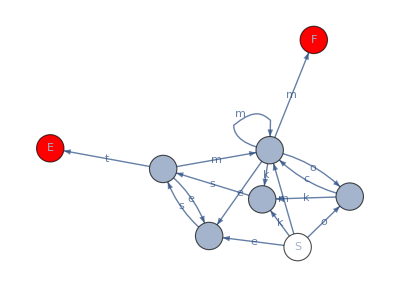

{mesmokst,mesmocmkst,mesmkst}

```mathematica
(* Define the function that will print the finite state automaton graph *)
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.55,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{q0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
];

(* Define the transition function of Pacman *)
δ = Association[
{"S", "m"}-> {"A"},
{"S", "e"}-> {"B"},
{"S", "o"}-> {"C"},
{"S", "k"}-> {"D"},
{"A", "m"} -> {"F", "A"},
{"A", "e"} -> {"B"},
{"A", "o"} -> {"C"},
{"A", "k"} -> {"D"},
{"B", "s"} -> {"U"},
{"C", "c"} -> {"A"},
{"C", "k"} -> {"D"},
{"D", "s"} -> {"U"},
{"U", "m"} -> {"A"},
{"U", "e"} -> {"B"},
{"U", "t"} -> {"E"}
];

(* Define functions to determine if a given string is accepted by Pacman *)
DeltaHat[δ_,q0_List,string_]:=FoldList[Union @@ Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]&,q0,Characters[string]];
IsValid[δ_, q0_List, qf_List, string_] := Intersection[Last[DeltaHat[δ, q0, string]], qf] ≠  {}

(* Define all the graph relations as a list of edges *)
edges = {S-> A,  S-> B, S-> "C", S-> "D", A-> F, A-> A, A-> B,  A-> "C", A-> "D", B-> U, "C"-> A, "C"-> "D", "D"-> U, U-> A, U-> B, U-> "E"};

(* Sets the list of all the involved states in the Pacman game *)
states = {S, A, B, "C", "D","E", U, F};

(* Define the initial state *)
q = S;

(* Define the final states *)
qF = {F,"E"};

(* Declare the alphabet of Pacman *)
alphabet = {"m","o","c","e","k","t","s"};

(* Generates a set with possible combinations *)
languages =  {"mesmokst", "mesmocmkst", "mesmkst", "mskts", "mkstk"};

(* Test a valid string *)
DeltaHat[δ,{"S"},"mesmokst"]

(* Show the graph *)
ShowGraphFA[edges, states, q, qF, {"m", "e", "o", "k", "m", "m", "e", "o", "k", "s", "c", "k", "s", "m", "e", "t"}]

(* Show valid languages *)
Select[Map[StringJoin, languages], IsValid[δ,{"S"},qF,#]&]
```